```mathematica
(*Mathematica*)
```

```mathematica
(*http://classes.yale.edu/fractals/IntroToFrac/DrivenIFS/DNADrIFS/DNADrIFS.html*)Clear[f,g,h,k,s0,ff,ll,kk,mm,a,g3,ga,x,y,w]
```

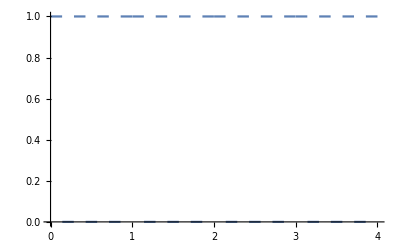

```mathematica
ff[x_]:=1/2+I*(ArcTanh[Exp[-7 I π*Mod[x,1]]]-ArcTanh[Exp[7 I π*Mod[x,1]]])/Pi
Plot[ff[x],{x,0,4}]
```

```mathematica
s0=N[Log[2]/Log[5]];
```

```mathematica
kk[x_]=N[Re[Sum[ff[5^k*x]/5^(s0*k),{k,0,20}]]];
ll[x_]=N[Re[Sum[ff[5^k*(x)+1/2]/5^(s0*k),{k,0,20}]]];
mm[x_]=N[Re[Sum[ff[5^k*(x)-1/2]/5^(s0*k),{k,0,20}]]];
```

```mathematica
n0=1000000;
a=Union[ParallelTable[{ll[t],kk[t],t},{t,0,1,1/n0}]];
b0=Length[a];
b=Delete[Delete[a,1],b0-1];
```

```mathematica
g1=ListPointPlot3D[a,PlotRange->All,AspectRatio->Automatic,Axes->False,PlotStyle->PointSize[0.002],ImageSize->{2000,2000},ColorFunction->"Rainbow",ViewPoint->{2,2,2},Background->Black];
```

```mathematica
Export["Biscuit_Squarewave2nd_3d_1000000_g1.jpg",g1]
```

Biscuit_Squarewave2nd_3d_1000000_g1.jpg

```mathematica
g2=Show[g1,ViewPoint->{1.3, -2.4, 2.},ImageSize->{2000,2000}];
```

```mathematica
Export["Biscuit_Squarewave2nd_3d_1000000_g2.jpg",g2]
```

Biscuit_Squarewave2nd_3d_1000000_g2.jpg

```mathematica
g3=Show[g1,ViewPoint->Front,ImageSize->{2000,2000}];
```

```mathematica
Export["Biscuit_Squarewave2nd_3d_1000000_g3.jpg",g3]
```

Biscuit_Squarewave2nd_3d_1000000_g3.jpg

```mathematica
g4=Show[g1,ViewPoint->Above,ImageSize->{2000,2000}];
```

```mathematica
Export["Biscuit_Squarewave2nd_3d_1000000_g4.jpg",g4]
```